```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/home/zack/oscillators/faraday

Single run plots

./faraday.py --geometry box --filebase data/boxinhomogeneous --xmesh 34 --zmesh 10 --ymesh 5 --samp 1.75

{4.,1.,2.}

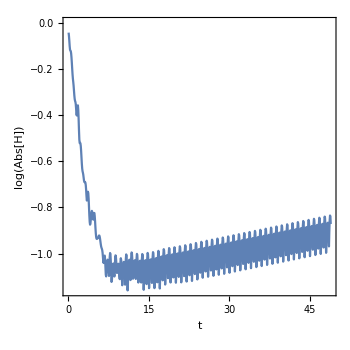
-Graphics- | -Graphics- | -Graphics-

24.000000 1.000000 0.500000 0.267610 4.442883

```mathematica
filebase="data/boxinhomogeneous";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],3],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
steps=ToExpression[lst[[FirstPosition[lst,"Steps"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
width=ToExpression[lst[[FirstPosition[lst,"Width"][[1]]+1]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
lst[[1]]
{length,width,height}
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],4];
contop=Cases[con,u_/;Length[Intersection[top,u]]==3];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==3];
sides1=Flatten[Join[Position[mesh[[-1]],u_/;Length[u]>0&&u[[1]]==0],Position[mesh[[-1]],u_/;Length[u]>0&&u[[1]]==length]]];
sides2=Flatten[Join[Position[mesh[[-1]],u_/;Length[u]>0&&u[[2]]==0],Position[mesh[[-1]],u_/;Length[u]>0&&u[[2]]==width]]];
consides1=Cases[con,u_/;Length[Intersection[sides1,u]]≥3];
consides2=Cases[con,u_/;Length[Intersection[sides2,u]]≥3];
m=Length[mesh];
mesh2=mesh[[m]];
p=Grid[{{ListPlot[Transpose[{Range[m]/steps,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],rasterizeBackground[Show[ListDensityPlot[mesh2[[top]],PlotRange->All,InterpolationOrder->10,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,y},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Graphics[Line[{mesh2[[#[[1]],{1,2}]],mesh2[[#[[2]],{1,2}]]}]&/@DeleteDuplicates[Flatten[Subsets[#,{2}]&/@(Intersection[#,top]&/@contop),1]]],ListPlot[{mesh2[[Complement[top,top2],{1,2}]],mesh2[[top2,{1,2}]]},PlotStyle->{Directive[Black,PointSize[0.02]],Directive[LightGray,PointSize[0.02]]}]]],Rasterize[Graphics3D[{Sphere[#,0.025]&/@mesh2[[top]],Sphere[#,0.025]&/@mesh2[[bottom]],Sphere[#,0.025]&/@mesh2[[sides1]],Sphere[#,0.025]&/@mesh2[[sides2]],EdgeForm[Directive[Black,Opacity[0.5]]],FaceForm[Directive[Opacity[0.5],Blue]],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides1]&/@consides1),Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides2]&/@consides2),Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,top]&/@contop),FaceForm[ColorData[97,"ColorList"][[2]]],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,bottom]&/@conbottom)},Boxed->False,ImageSize->500,PlotRange->{All,All,All},ViewPoint->{0, -3, 1}],ImageSize->500]}}]
lst[[-1]]
```

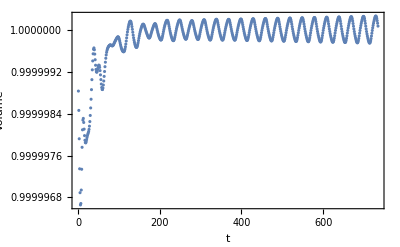

```mathematica
(* Numerical loss of fluid volume during saturation, but not too bad...*)
ListPlot[Total[#[[top,3]]]/(Length[top]*height)&/@mesh,Axes->False,Frame->True,FrameLabel->{t,"Volume"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All]
```

```mathematica
modes=Sort[Flatten[Table[((n1*Pi/width)^2+(n2*Pi/length)^2)^(1/2),{n1,0,5},{n2,0,5}]]]
frequencies=2*(980*#*Tanh[height*#]*(1+72/980*#^2))^(1/2)/(2*Pi)&/@modes
modes2=SortBy[Flatten[Table[{#,(980*#*Tanh[height*#]*(1+72/980*#^2))^(1/2)/(2*Pi),{n1,n2}}&@(((n1*Pi/width)^2+(n2*Pi/length)^2)^(1/2)),{n1,0,5},{n2,0,5}],1],First]
```

{0.,0.785398,1.5708,2.35619,3.14159,3.14159,3.23828,3.51241,3.92699,3.92699,4.44288,5.029,6.28319,6.33208,6.47656,6.71044,7.02481,7.40943,9.42478,9.45745,9.55478,9.71484,9.93459,10.2102,12.5664,12.5909,12.6642,12.7854,12.9531,13.1657,15.708,15.7276,15.7863,15.8837,16.019,16.1914}

{0.,8.64676,13.5484,18.1475,23.1977,23.1977,23.8594,25.7853,28.8395,28.8395,32.8775,37.7784,49.33,49.8084,51.2339,53.5788,56.8019,60.8539,83.9231,84.3212,85.5115,87.4831,90.2184,93.6945,125.396,125.744,126.785,128.515,130.923,133.997,172.725,173.038,173.974,175.531,177.703,180.482}

{{0.,0.,{0,0}},{0.785398,4.32338,{0,1}},{1.5708,6.7742,{0,2}},{2.35619,9.07373,{0,3}},{3.14159,11.5989,{0,4}},{3.14159,11.5989,{1,0}},{3.23828,11.9297,{1,1}},{3.51241,12.8926,{1,2}},{3.92699,14.4197,{0,5}},{3.92699,14.4197,{1,3}},{4.44288,16.4388,{1,4}},{5.029,18.8892,{1,5}},{6.28319,24.665,{2,0}},{6.33208,24.9042,{2,1}},{6.47656,25.617,{2,2}},{6.71044,26.7894,{2,3}},{7.02481,28.401,{2,4}},{7.40943,30.4269,{2,5}},{9.42478,41.9616,{3,0}},{9.45745,42.1606,{3,1}},{9.55478,42.7558,{3,2}},{9.71484,43.7416,{3,3}},{9.93459,45.1092,{3,4}},{10.2102,46.8472,{3,5}},{12.5664,62.6982,{4,0}},{12.5909,62.872,{4,1}},{12.6642,63.3927,{4,2}},{12.7854,64.2574,{4,3}},{12.9531,65.4614,{4,4}},{13.1657,66.9986,{4,5}},{15.708,86.3627,{5,0}},{15.7276,86.5189,{5,1}},{15.7863,86.9871,{5,2}},{15.8837,87.7655,{5,3}},{16.019,88.8514,{5,4}},{16.1914,90.241,{5,5}}}

Animation

```mathematica
m0=Length[mesh]-750;
m1=Length[mesh];
If[!DirectoryQ["boxanimation"],CreateDirectory["boxanimation"]]
Monitor[Do[
acc=ToExpression[StringSplit[lst[[-1]]," "]][[2]];
freq=ToExpression[StringSplit[lst[[-1]]," "]][[1]];
amp=980*acc/(2*Pi*freq)^2;
z0=amp*Sin[2*Pi*m/15];
mesh2={#[[1]],#[[2]],z0+#[[3]]}&/@mesh[[m]];
p=Grid[{{ListPlot[{Transpose[{Range[Length[norms]]/15,Log[norms]/Log[10]}],Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}]},Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->{Directive[LightGray,AbsoluteThickness[1]],Directive[Black,AbsoluteThickness[2]]},FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListDensityPlot[mesh2[[top]],PlotRange->All,InterpolationOrder->10,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,y},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Graphics[Line[{mesh2[[#[[1]],{1,2}]],mesh2[[#[[2]],{1,2}]]}]&/@DeleteDuplicates[Flatten[Subsets[#,{2}]&/@(Intersection[#,top]&/@contop),1]]],ListPlot[{mesh2[[Complement[top,top2],{1,2}]],mesh2[[top2,{1,2}]]},PlotStyle->{Directive[Black,PointSize[0.02]],Directive[LightGray,PointSize[0.02]]}]],Graphics3D[{Sphere[#,0.025]&/@mesh2[[top]],Sphere[#,0.025]&/@mesh2[[bottom]],Sphere[#,0.025]&/@mesh2[[sides1]],Sphere[#,0.025]&/@mesh2[[sides2]],EdgeForm[Directive[Black,Opacity[0.5]]],FaceForm[Directive[Opacity[0.5],Blue]],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides1]&/@consides1),Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides2]&/@consides2),Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,top]&/@contop),FaceForm[ColorData[97,"ColorList"][[2]]],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,bottom]&/@conbottom)},Boxed->False,ImageSize->500,PlotRange->{All,All,All},ViewPoint->{0, -3, 1}]}}];
Export["boxanimation/"<>IntegerString[m-m0,10,4]<>".png",p,ImageResolution->100];,{m,m0,m1}],N[(m-m0)/(m1-m0)]]
```

Sweep plots

```mathematica
filebase="sweeps/sb1"
growth1=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,50}],1];
Amin=Min[growth1[[All,2]]];
Amax=Max[growth1[[All,2]]];
fmin=Min[growth1[[All,1]]];
fmax=Max[growth1[[All,1]]];
kmin=Min[growth1[[All,5]]];
kmax=Max[growth1[[All,5]]];
max=Max[growth1[[All,4]]];
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
p1=Grid[{{Show[rasterizeBackground[Show[ListDensityPlot[growth1[[All,{1,2,4}]],InterpolationOrder->0,PlotRange->{All,All,{0.0,max}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Growth Rate"}},Epilog->{Inset[BarLegend[{"Rainbow",{0,max}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]}],Plot[2*(ν1+ν3*k^2+ν2*k*Tanh[k*height])*(1+σ/g*k^2)/(k*Tanh[k*height]*(g+σ*k^2))^(1/2)/.FindRoot[2*Pi*f/2==(k*Tanh[k*height]*(g+σ*k^2))^(1/2), {k,1.0}],{f,fmin,fmax},PlotStyle->Directive[Black]]]],PlotRangeClipping->False,ImageSize->400,ImagePadding->{{65,100},{50,50}}],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,3}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.0,1.1}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/1.0]&),ColorFunctionScaling->False,FrameLabel->{{Aω^2,None},{f,"Frequency"}},ImageSize->300],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,5}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.9*kmin,1.1*kmax}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
```

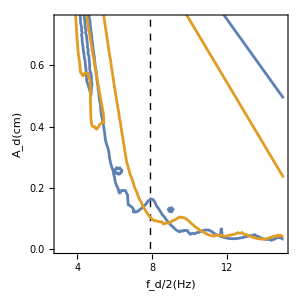
-Graphics- | -Graphics-

plots/boxgap.pdf

```mathematica
gap=2*Pi/length*5/4;
filebase="data/boxinhomogeneous";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],3],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
steps=ToExpression[lst[[FirstPosition[lst,"Steps"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
width=ToExpression[lst[[FirstPosition[lst,"Width"][[1]]+1]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
p2=Rasterize[Graphics3D[{Sphere[#,0.025]&/@mesh2[[top]],Sphere[#,0.025]&/@mesh2[[bottom]],Sphere[#,0.025]&/@mesh2[[sides1]],Sphere[#,0.025]&/@mesh2[[sides2]],EdgeForm[Directive[Black,Opacity[0.5]]],FaceForm[Directive[Opacity[0.5],Blue]],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides1]&/@consides1),Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides2]&/@consides2),Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,top]&/@contop),FaceForm[ColorData[97,"ColorList"][[2]]],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,bottom]&/@conbottom)},Boxed->False,ImageSize->300,PlotRange->{All,All,All},ViewPoint->{0, -3, 1}],ImageSize->300];
filebases={"sweeps/sb1","sweeps/sb2"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
interpolations[f_,a_]=Table[Interpolation[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],InterpolationOrder->1][f,a],{i,1,Length[sweeps]}];p3=Show@@Table[ContourPlot[interpolations[f,a][[i]],{f,2.63,15},{a,0.000552,1.8},Contours->{0.0},PlotRange->{{3,15},{0,0.75}},ContourShading->None,ContourStyle->{Directive[ColorData[97,"ColorList"][[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.6,0.2}],Table[{i,""},{i,0,0.6,0.2}]},{Table[{i,i},{i,4,14,2}],Table[{i,""},{i,4,14,2}]}},Prolog->{Black,Dashed,Line[{{(g*gap*Tanh[gap*height]*(1+σ/g*gap^2))^(1/2)/(2*Pi),0},{(g*gap*Tanh[gap*height]*(1+σ/g*gap^2))^(1/2)/(2*Pi),2}}]}],{i,1,Length[sweeps]}];
p=Grid[{{p2,p3}}]
Export["plots/boxgap.pdf",p]
```

STL file generation

```mathematica
filebase="box";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],3],meshpoints];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
steps=ToExpression[lst[[FirstPosition[lst,"Steps"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
width=ToExpression[lst[[FirstPosition[lst,"Width"][[1]]+1]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
lst[[1]]
{length,width,height}
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],4];
contop=Cases[con,u_/;Length[Intersection[top,u]]==3];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==3];
sides1=Flatten[Join[Position[mesh[[-1]],u_/;Length[u]>0&&u[[1]]==0],Position[mesh[[-1]],u_/;Length[u]>0&&u[[1]]==length]]];
sides2=Flatten[Join[Position[mesh[[-1]],u_/;Length[u]>0&&u[[2]]==0],Position[mesh[[-1]],u_/;Length[u]>0&&u[[2]]==width]]];
consides1=Cases[con,u_/;Length[Intersection[sides1,u]]≥3];
consides2=Cases[con,u_/;Length[Intersection[sides2,u]]≥3];
m=Length[mesh];
mesh2=mesh[[m]];
Rasterize[Graphics3D[{Sphere[#,0.025]&/@mesh2[[top]],Sphere[#,0.025]&/@mesh2[[bottom]],Sphere[#,0.025]&/@mesh2[[sides1]],Sphere[#,0.025]&/@mesh2[[sides2]],EdgeForm[Directive[Black,Opacity[0.5]]],FaceForm[Directive[Opacity[0.5],Blue]],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides1]&/@consides1),Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,sides2]&/@consides2),Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,top]&/@contop),FaceForm[ColorData[97,"ColorList"][[2]]],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@(Intersection[#,bottom]&/@conbottom)},Boxed->False,ImageSize->500,PlotRange->{All,All,All},ViewPoint->{0, -3, 1}],ImageSize->300]
```

./faraday.py --filebase box --geometry box --xmesh 15 --zmesh 5 --ymesh 5 --time 0 --height 0.5 --width 1 --length 4 --samp 0.4 --contact slip --refinement 2

{4.,1.,0.5}

-Graphics-

```mathematica
min=Min[mesh2[[All,3]]];
edge=0.1;
cubestl={Cross[#[[1]]-#[[2]],#[[3]]-#[[1]]]/Norm[Cross[#[[1]]-#[[2]],#[[3]]-#[[1]]]],#[[1]],#[[2]],#[[3]]}&/@{{{-edge,-edge,height},{-edge,-edge,min-edge},{-edge,width+edge,min-edge}},{{-edge,width+edge,height},{-edge,-edge,height},{-edge,width+edge,min-edge}},{{length+edge,-edge,min-edge},{length+edge,-edge,height},{length+edge,width+edge,min-edge}},{{length+edge,-edge,height},{length+edge,width+edge,height},{length+edge,width+edge,min-edge}},
{{length+edge,width+edge,height},{-edge,width+edge,min-edge},{length+edge,width+edge,min-edge}},{{-edge,width+edge,min-edge},{length+edge,width+edge,height},{-edge,width+edge,height}},{{-edge,-edge,min-edge},{length+edge,-edge,height},{length+edge,-edge,min-edge}},{{length+edge,-edge,height},{-edge,-edge,min-edge},{-edge,-edge,height}},{{length+edge,width+edge,min-edge},{-edge,-edge,min-edge},{length+edge,-edge,min-edge}},{{-edge,-edge,min-edge},{length+edge,width+edge,min-edge},{-edge,width+edge,min-edge}},{{-edge,-edge,height},{-edge,width+edge,height},{0,0,height}},{{-edge,width+edge,height},{0,width,height},{0,0,height}},{{length+edge,width+edge,height},{length+edge,-edge,height},{length,0,height}},{{length,width,height},{length+edge,width+edge,height},{length,0,height}},{{length+edge,-edge,height},{-edge,-edge,height},{0,0,height}},{{length,0,height},{length+edge,-edge,height},{0,0,height}},{{-edge,width+edge,height},{length+edge,width+edge,height},{0,width,height}},{{length+edge,width+edge,height},{length,width,height},{0,width,height}}};
sides1stl=Table[n=Cross[mesh2[[u[[1]]]]-mesh2[[u[[2]]]],mesh2[[u[[3]]]]-mesh2[[u[[1]]]]]/Norm[Cross[mesh2[[u[[1]]]]-mesh2[[u[[2]]]],mesh2[[u[[1]]]]-mesh2[[u[[3]]]]]];Flatten[{If[(mesh2[[u[[1]],1]]==0.&&n[[1]]<0)||(mesh2[[u[[1]],1]]==length&&n[[1]]>0),-n,n],mesh2[[u[[1]]]],mesh2[[u[[2]]]],mesh2[[u[[3]]]]}],{u,(Intersection[#,sides1]&/@consides1)}];
sides2stl=Table[n=Cross[mesh2[[u[[1]]]]-mesh2[[u[[2]]]],mesh2[[u[[3]]]]-mesh2[[u[[1]]]]]/Norm[Cross[mesh2[[u[[1]]]]-mesh2[[u[[2]]]],mesh2[[u[[1]]]]-mesh2[[u[[3]]]]]];Flatten[{If[(mesh2[[u[[1]],2]]==0.&&n[[2]]<0)||(mesh2[[u[[1]],2]]==width&&n[[2]]>0),-n,n],mesh2[[u[[1]]]],mesh2[[u[[2]]]],mesh2[[u[[3]]]]}],{u,(Intersection[#,sides2]&/@consides2)}];
bottomstl=Table[n=Cross[mesh2[[u[[1]]]]-mesh2[[u[[2]]]],mesh2[[u[[3]]]]-mesh2[[u[[1]]]]]/Norm[Cross[mesh2[[u[[1]]]]-mesh2[[u[[2]]]],mesh2[[u[[1]]]]-mesh2[[u[[3]]]]]];Flatten[{If[n[[3]]>0.,n,-n],mesh2[[u[[1]]]],mesh2[[u[[2]]]],mesh2[[u[[3]]]]}],{u,(Intersection[#,bottom]&/@conbottom)}];
stl=Join[bottomstl,sides1stl,sides2stl,cubestl];
file=OpenWrite["test.stl",BinaryFormat->True];
BinaryWrite[file,ConstantArray[0,80],"UnsignedInteger8",ByteOrdering->-1];
BinaryWrite[file,Length[stl],"Integer32",ByteOrdering->-1];
Do[BinaryWrite[file,triangle,"Real32",ByteOrdering->-1];BinaryWrite[file,0,"UnsignedInteger16",ByteOrdering->-1];,{triangle,stl}]
Close[file]
```

test.stl

```mathematica
file=OpenRead["test.stl",BinaryFormat->True]
BinaryReadList[file,"UnsignedInteger8",80]
len=BinaryRead[file,"Integer32"]
stl2=Table[triangle=BinaryReadList[file,"Real32",12];attribute=BinaryRead[file,"UnsignedInteger16"];triangle,{i,1,len}];
Close[file]
Rasterize[Graphics3D[{{Sphere[#[[2]],0.025],Sphere[#[[3]],0.025],Sphere[#[[4]],0.025]}&/@(Partition[#,3]&/@stl2),Arrow[{Mean[#[[2;;4]]],Mean[#[[2;;4]]]+0.0*#[[1]]}]&/@(Partition[#,3]&/@stl2),EdgeForm[Directive[Black,Opacity[0.5]]],FaceForm[Directive[Opacity[0.5],Blue]],Triangle[{#[[2]],#[[3]],#[[4]]}]&/@(Partition[#,3]&/@stl2)},Boxed->False,ImageSize->600,PlotRange->{All,All,All},ViewPoint->{0, -3, 1}]]
```

InputStream[…]

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

4978

test.stl

-Graphics-